```mathematica
ClearAll["Global`*"]
```

```mathematica
β=0.25;
Ω=1.0;
Γ = 0.25  ;
δ = Ω^2/(2 β^2);

Δ[t_]:=β^2 t;

t0=-10 Ω/β^2;
tf=10 Ω/β^2;
```

```mathematica
a = (I-Ω^2/(2 β))*1/2;
```

```mathematica
DSolve[v''[τ]+(τ^2/4-a) v[τ]==0,v,τ]
```

```mathematica
eq=v''[τ]+(τ^2/4-(I-δ)/2)v[τ]==0;
DSolve[eq,v,τ]
```

{{v→Function[{τ},C[2] ParabolicCylinderD[(ⅈ δ)/2,(-1)^(3/4) τ]+C[1] ParabolicCylinderD[-1/2 ⅈ (-2 ⅈ+δ),(-1)^(1/4) τ]]}}

```mathematica
v1[τ_]=ParabolicCylinderD[-1-I δ/2,Exp[I Pi/4] τ];
v2[τ_]=ParabolicCylinderD[I δ/2,Exp[3 I Pi/4] τ];
```

```mathematica
M={{v1[τ0],v2[τ0]},{v1'[τ0],v2'[τ0]}};
b={1,I τ0/2};
```

```mathematica
{c1,c2}=LinearSolve[M,b];
```

```mathematica
c1
```

((-1)^(3/4) ParabolicCylinderD[1+(ⅈ δ)/2,ⅇ^((3 ⅈ π)/4) τ0]+ⅈ τ0 ParabolicCylinderD[(ⅈ δ)/2,ⅇ^((3 ⅈ π)/4) τ0])/((-1)^(3/4) ParabolicCylinderD[-1-(ⅈ δ)/2,ⅇ^((ⅈ π)/4) τ0] ParabolicCylinderD[1+(ⅈ δ)/2,ⅇ^((3 ⅈ π)/4) τ0]+ⅈ τ0 ParabolicCylinderD[-1-(ⅈ δ)/2,ⅇ^((ⅈ π)/4) τ0] ParabolicCylinderD[(ⅈ δ)/2,ⅇ^((3 ⅈ π)/4) τ0]-(-1)^(1/4) ParabolicCylinderD[-(ⅈ δ)/2,ⅇ^((ⅈ π)/4) τ0] ParabolicCylinderD[(ⅈ δ)/2,ⅇ^((3 ⅈ π)/4) τ0])

```mathematica
FullSimplify[c1]
```

```mathematica
c2
```

-(((-1)^(1/4) ParabolicCylinderD[-(ⅈ δ)/2,ⅇ^((ⅈ π)/4) τ0])/((-1)^(3/4) ParabolicCylinderD[-1-(ⅈ δ)/2,ⅇ^((ⅈ π)/4) τ0] ParabolicCylinderD[1+(ⅈ δ)/2,ⅇ^((3 ⅈ π)/4) τ0]+ⅈ τ0 ParabolicCylinderD[-1-(ⅈ δ)/2,ⅇ^((ⅈ π)/4) τ0] ParabolicCylinderD[(ⅈ δ)/2,ⅇ^((3 ⅈ π)/4) τ0]-(-1)^(1/4) ParabolicCylinderD[-(ⅈ δ)/2,ⅇ^((ⅈ π)/4) τ0] ParabolicCylinderD[(ⅈ δ)/2,ⅇ^((3 ⅈ π)/4) τ0]))

```mathematica
c1Num = ((-1)^(3/4) ParabolicCylinderD[1+(ⅈ δ)/2,ⅇ^((3 ⅈ π)/4) τ0]+ⅈ τ0 ParabolicCylinderD[(ⅈ δ)/2,ⅇ^((3 ⅈ π)/4) τ0]);
c1Den[τ_] := -(-1)^(1/4) ParabolicCylinderD[-(ⅈ δ)/2,(-1)^(1/4) τ] ParabolicCylinderD[(ⅈ δ)/2,(-1)^(3/4) τ]+ParabolicCylinderD[-1-(ⅈ δ)/2,(-1)^(1/4) τ] ((-1)^(3/4) ParabolicCylinderD[1+(ⅈ δ)/2,(-1)^(3/4) τ]+ⅈ τ ParabolicCylinderD[(ⅈ δ)/2,(-1)^(3/4) τ]);

c2Num = -(-1)^(1/4) ParabolicCylinderD[-(ⅈ δ)/2,ⅇ^((ⅈ π)/4) τ0];

c2Den[τ_] := -(-1)^(1/4) ParabolicCylinderD[-(ⅈ δ)/2,(-1)^(1/4) τ] ParabolicCylinderD[(ⅈ δ)/2,(-1)^(3/4) τ]+ParabolicCylinderD[-1-(ⅈ δ)/2,(-1)^(1/4) τ] ((-1)^(3/4) ParabolicCylinderD[1+(ⅈ δ)/2,(-1)^(3/4) τ]+ⅈ τ ParabolicCylinderD[(ⅈ δ)/2,(-1)^(3/4) τ]);
```

```mathematica
τ0 = β t0; τf = β tf;
```

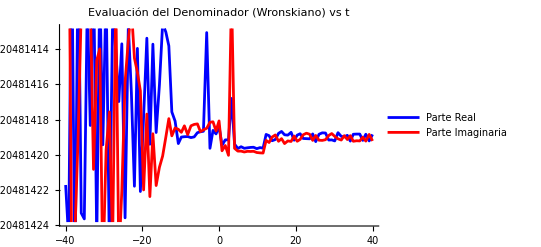

```mathematica
Plot[
{Re[c2Den[τ]],Im[c2Den[τ]]},
{τ,τ0,τf},PlotStyle->{Blue,Red},
WorkingPrecision->40,
PlotLegends->{"Parte Real","Parte Imaginaria"},
PlotLabel->"Evaluación del Denominador (Wronskiano) vs t"]
```

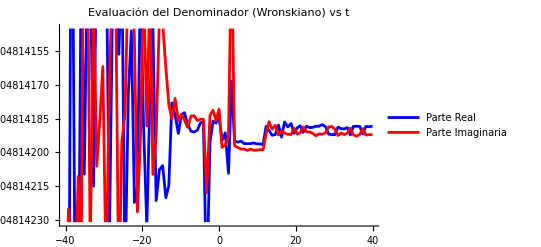

```mathematica
Plot[
{Re[c1Den[τ]],Im[c1Den[τ]]},
{τ,τ0,τf},PlotStyle->{Blue,Red},
PlotLegends->{"Parte Real","Parte Imaginaria"},
PlotLabel->"Evaluación del Denominador (Wronskiano) vs t"]
```

```mathematica
FullSimplify[ Wronskian[{v1[τ],v2[τ]},τ]]
```

(-1)^(1/4) ParabolicCylinderD[-(ⅈ δ)/2,(-1)^(1/4) τ] ParabolicCylinderD[(ⅈ δ)/2,(-1)^(3/4) τ]-ParabolicCylinderD[-1-(ⅈ δ)/2,(-1)^(1/4) τ] ((-1)^(3/4) ParabolicCylinderD[1+(ⅈ δ)/2,(-1)^(3/4) τ]+ⅈ τ ParabolicCylinderD[(ⅈ δ)/2,(-1)^(3/4) τ])

```mathematica
Wτ[τ_]:=(-1)^(1/4) ParabolicCylinderD[-(ⅈ δ)/2,(-1)^(1/4) τ] ParabolicCylinderD[(ⅈ δ)/2,(-1)^(3/4) τ]-ParabolicCylinderD[-1-(ⅈ δ)/2,(-1)^(1/4) τ] ((-1)^(3/4) ParabolicCylinderD[1+(ⅈ δ)/2,(-1)^(3/4) τ]+ⅈ τ ParabolicCylinderD[(ⅈ δ)/2,(-1)^(3/4) τ])
```

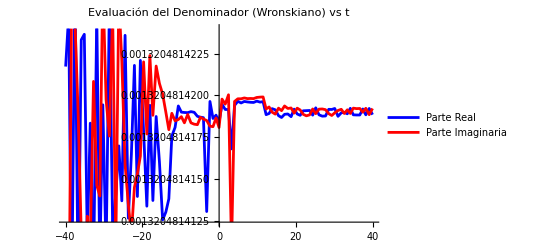

```mathematica
Plot[
{Re[Wτ[τ]], Im[Wτ[τ]]},
{τ,τ0,τf},PlotStyle->{Blue,Red},
WorkingPrecision->40,
PlotLegends->{"Parte Real","Parte Imaginaria"},
PlotLabel->"Evaluación del Denominador (Wronskiano) vs t"]
```

```mathematica
Wval=FullSimplify[c2Den[0]];
```

```mathematica
Wval
```

-0.00132048-0.00132048 ⅈ

```mathematica
c1Num / Wval
```

-810.08-931.598 ⅈ

```mathematica
c1
```

-810.08-931.598 ⅈ

```mathematica
FullSimplify[Inverse[M].b]
```

## Numerical Error Estimation

```mathematica
β=0.25;
Ω=1.0;
Γ = 0.25  ;
δ = Ω^2/(2β^2);

Δ[t_]:=β^2 t;
Δdot = β^2;

t0=-10 Ω/β^2;
tf=10 Ω/β^2;

τ0 = β*t0;
τf = β*tf;
τ[t_]:=β t;

a = (I-δ)*1/2;
```

### Analytical Solution (H.F Weber Equation)

```mathematica
ClearAll["Global`*"]
```

```mathematica
eq=v''[τ]+(τ^2/4-(I-δ)/2)v[τ]==0;
DSolve[eq,v,τ]
```

{{v→Function[{τ},C[2] ParabolicCylinderD[(ⅈ δ)/2,(-1)^(3/4) τ]+C[1] ParabolicCylinderD[-1/2 ⅈ (-2 ⅈ+δ),(-1)^(1/4) τ]]}}

```mathematica
v1[τ_]:=ParabolicCylinderD[-1-I δ/2,Exp[I Pi/4] τ];
v2[τ_]:=ParabolicCylinderD[I δ/2,Exp[3 I Pi/4] τ];
```

```mathematica
M={{v1[τ0],v2[τ0]},{v1'[τ0],v2'[τ0]}};
b={1,I τ0/2};
{C1,C2}=LinearSolve[M,b];
```

```mathematica
FullSimplify[C1]
```

-810.08-931.598 ⅈ

```mathematica
FullSimplify[C2]
```

71.5806-613.117 ⅈ

```mathematica
vAna[t_]:=C1 v1[τ[t]]+C2 v2[τ[t]];
```

### Numerical Solution

```mathematica
eqv={v''[t]+(Δ[t]^2/4+Ω^2/4- (I Δdot)/2)v[t]==0,v[t0]==1,v'[t0]==I/2 Δ[t0]};
vNum=NDSolveValue[eqv,v,{t,t0,tf},Method->{"StiffnessSwitching"}];
```

### Alpha Function

```mathematica
alphaNum[t_]:=Δ[t]/Ω+(2 I/Ω) vNum'[t]/vNum[t];
alphaAna[t_]:=Δ[t]/Ω+(2 I/Ω) vAna'[t]/vAna[t];
```

```mathematica
errorAlpha[t_]:=Abs[alphaNum[t]-alphaAna[t]];
RerrorAlpha[t_]:= errorAlpha[t]/Abs[alphaAna[t]];
```

### Error

```mathematica
err[t_] := Abs[vNum[t]-vAna[t]];
Rerr[t_] := err[t]/Abs[vAna[t]];
```

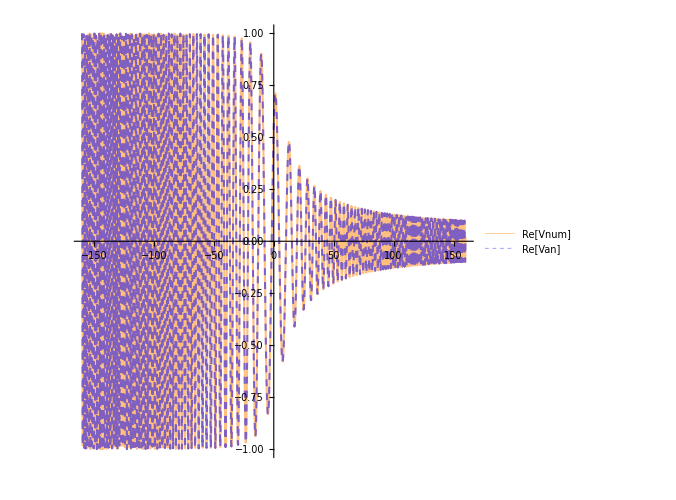

```mathematica
Plot[{Re[vNum[t]],Re[vAna[t]]},{t,t0,tf},
PlotStyle->{ Directive[Thickness[0.003], Orange, Opacity[0.5]], 
Directive[Dashed,Thickness[0.003],Blue, Opacity[0.5]]},
PlotLegends-> {"Re[Vnum]", "Re[Van]"},
AspectRatio->1, ImageSize->500]
```

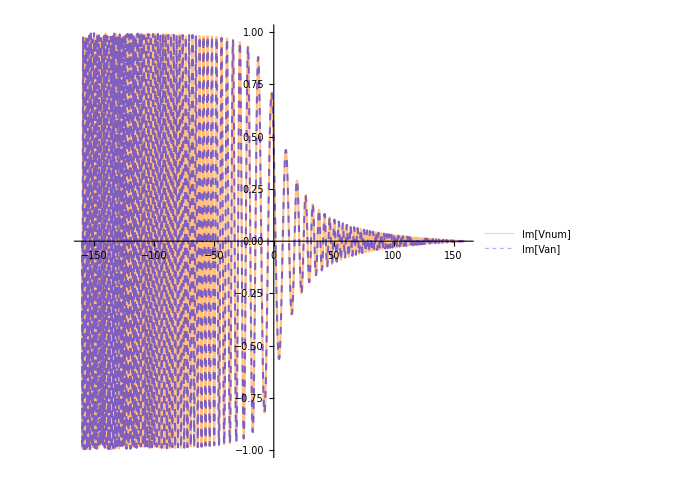

```mathematica
Plot[{Im[vNum[t]],Im[vAna[t]]},{t,t0,tf},
PlotStyle->{ Directive[Thickness[0.003], Orange, Opacity[0.5]], 
Directive[Dashed,Thickness[0.003],Blue, Opacity[0.5]]},
PlotLegends-> {"Im[Vnum]", "Im[Van]"},
AspectRatio->1, ImageSize->500]
```

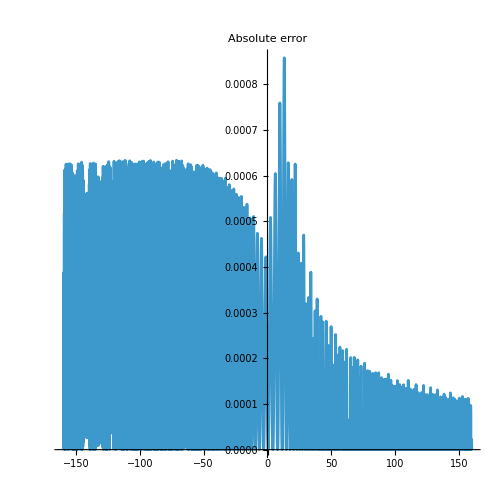

```mathematica
Plot[err[t],{t,t0,tf}, AspectRatio->1, ImageSize->500,
PlotLegends-> "Err", PlotLabel->"Absolute error"]
```

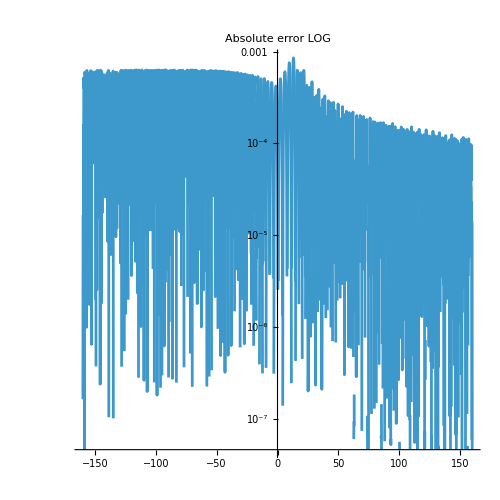

```mathematica
Plot[err[t],{t,t0,tf},ScalingFunctions->"Log", AspectRatio->1, ImageSize->500,
PlotLegends-> "Err", PlotLabel->"Absolute error LOG"]
```

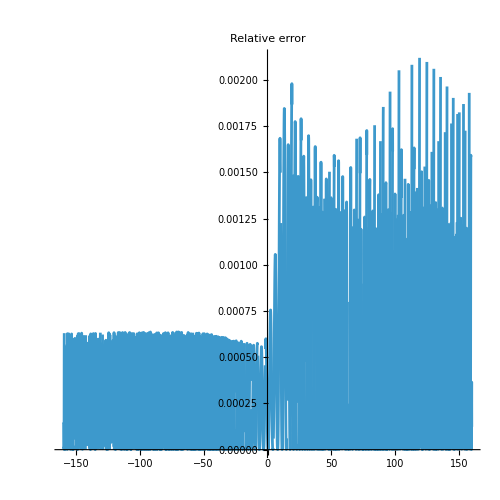

```mathematica
Plot[Rerr[t],{t,t0,tf}, AspectRatio->1, ImageSize->500,
PlotLegends-> "Relative error", PlotLabel->"Relative error"]
```

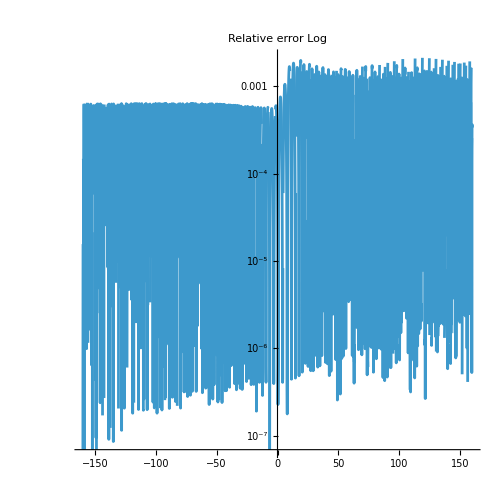

```mathematica
Plot[Rerr[t],{t,t0,tf}, AspectRatio->1, ImageSize->500,ScalingFunctions->"Log",
PlotLegends-> "Relative error Log", PlotLabel->"Relative error Log"]
```

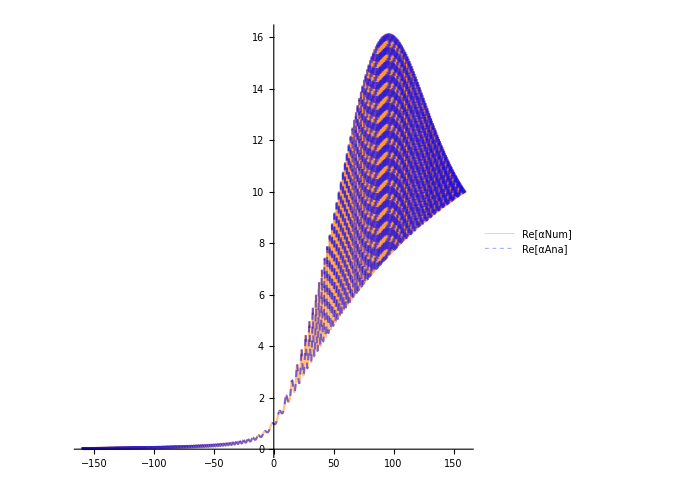

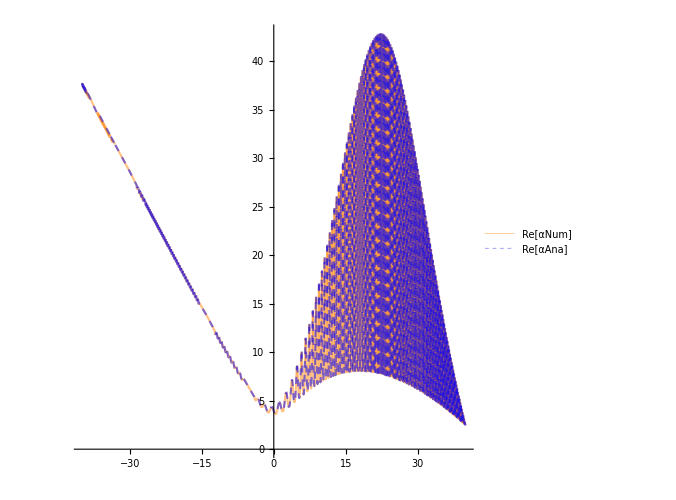

```mathematica
Plot[{Re[alphaNum[t]],Re[alphaAna[t]]},{t,t0,tf},
PlotStyle->{ Directive[Thickness[0.003], Orange, Opacity[0.5]], 
Directive[Dashed,Thickness[0.003],Blue, Opacity[0.5]]},
PlotLegends-> {"Re[αNum]", "Re[αAna]"},
AspectRatio->1, ImageSize->500]
```

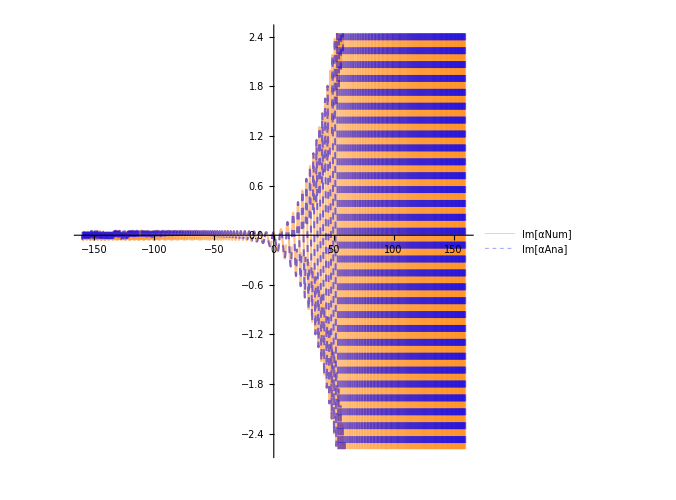

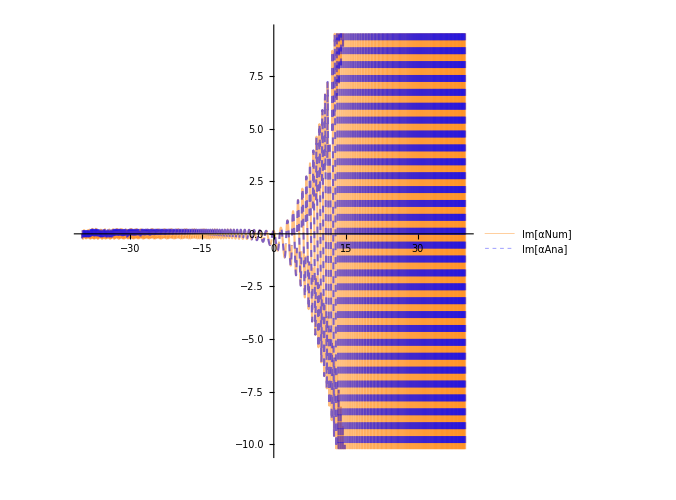

```mathematica
Plot[{Im[alphaNum[t]],Im[alphaAna[t]]},{t,t0,tf},
PlotStyle->{ Directive[Thickness[0.003], Orange, Opacity[0.5]], 
Directive[Dashed,Thickness[0.003],Blue, Opacity[0.5]]},
PlotLegends-> {"Im[αNum]", "Im[αAna]"},
AspectRatio->1, ImageSize->500]
```

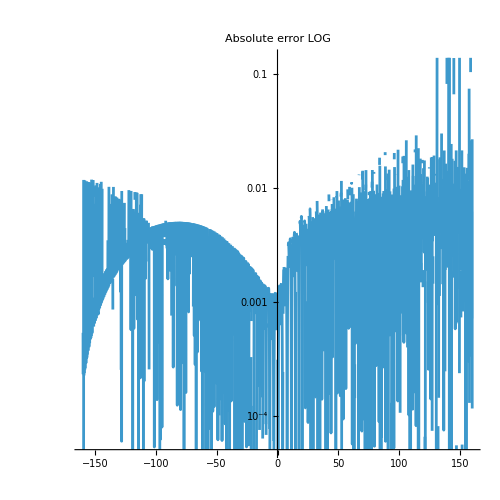

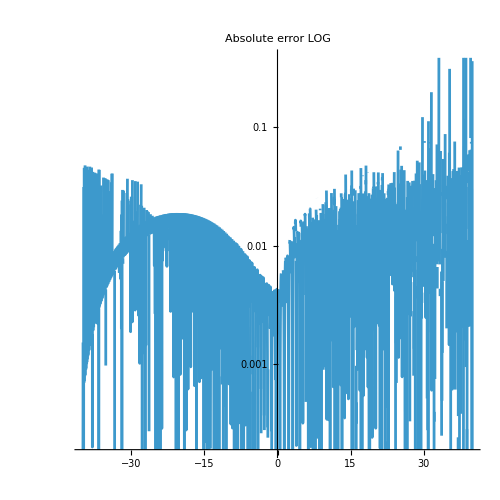

```mathematica
Plot[errorAlpha[t],{t,t0,tf},ScalingFunctions->"Log", AspectRatio->1, ImageSize->500,
PlotLegends-> "Err", PlotLabel->"Absolute error LOG"]
```

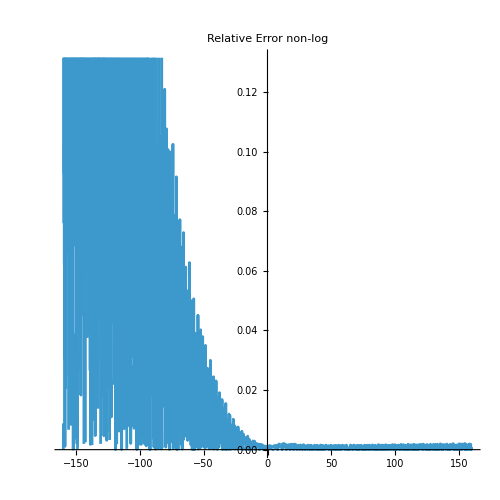

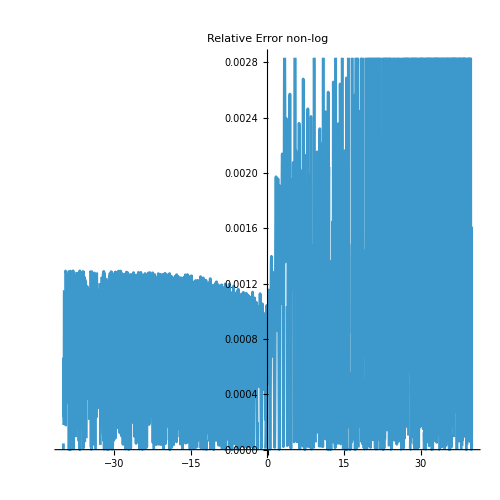

```mathematica
Plot[RerrorAlpha[t],{t,t0,tf}, AspectRatio->1, ImageSize->500,
PlotLegends-> "Relative Err", PlotLabel->"Relative Error non-log"]
```

## Comparison of Numerical Solutions

```mathematica
eqV = {v''[t] + (Ω^2/4+ Δ[t]^2/4- I Δdot/2)v[t] == 0, v[t0]== 1, v'[t0]== I/2 Δ[t0]};
vSol=NDSolveValue[eqV,v,{t,t0,tf},Method->{"StiffnessSwitching"}];
alphaMas1[t_]:= Δ[t]/Ω +((2 I)/Ω) vSol'[t]/vSol[t];
```

```mathematica
eqU={u''[t]+I Δ[t] u'[t]+((Ω^2) u[t])/4==0,u[t0]==1,u'[t0]==0};
uSol=NDSolveValue[eqU,u,{t,t0,tf},Method->{"StiffnessSwitching"}];
alphaMas2[t_]:=(2 I/Ω)uSol'[t]/uSol[t];
```

```mathematica
eqPlus={αp'[t]==-I(Δ[t] αp[t] - Ω/2(αp[t]^2 - 1)),αp[t0]==0};
alphaMas3=NDSolveValue[eqPlus,αp,{t,t0,tf},Method->{"StiffnessSwitching"}];
```

```mathematica
ecuacionesOptimizadas={x'[t]==I*((Ω/2)*x[t]-(β^2/2)*t)*x[t]*2-(I*Ω/2)*(1+x[t]^2),y'[t]==(I/2)*(Ω*x[t]-(β^2)*t),z'[t]==-(I*Ω/2)*Exp[2*y[t]],x[t0]==0,y[t0]==0,z[t0]==0}; 
{alphaMas4, alphaZ, alphaMin}=NDSolveValue[ecuacionesOptimizadas,{x,y, z},{t,t0, tf},AccuracyGoal->10, PrecisionGoal->10];
```

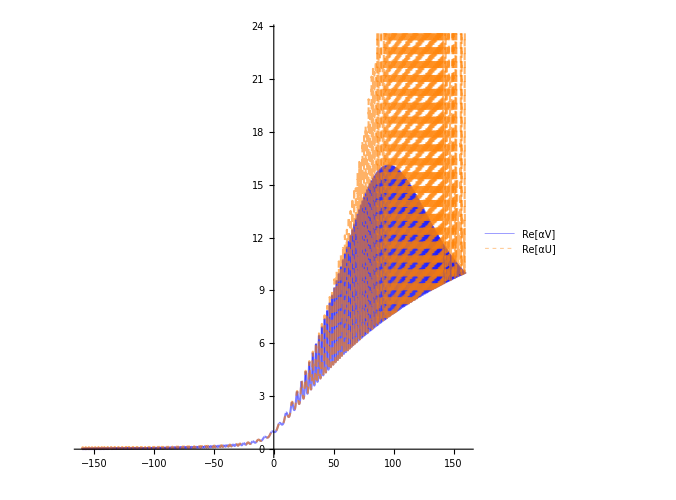

```mathematica
Plot[{Re[alphaMas1[t]],Re[alphaMas4[t]]},{t,t0,tf},
PlotStyle->{ Directive[Thickness[0.003], Blue, Opacity[0.5]], 
Directive[Dashed,Thickness[0.003],Orange, Opacity[0.6]]},
PlotLegends-> {"Re[αV]", "Re[αU]", "Re[αRicc]"},
AspectRatio->1, ImageSize->500]
```

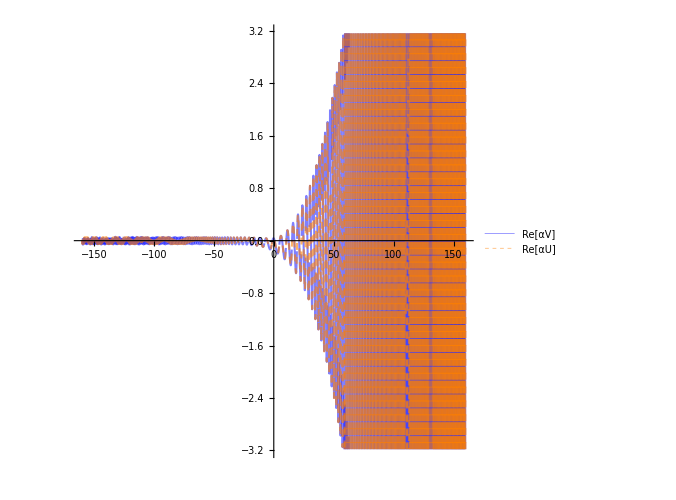

```mathematica
Plot[{Im[alphaMas1[t]],Im[alphaMas4[t]]},{t,t0,tf},
PlotStyle->{ Directive[Thickness[0.003], Blue, Opacity[0.5]], 
Directive[Dashed,Thickness[0.003],Orange, Opacity[0.6]]},
PlotLegends-> {"Re[αV]", "Re[αU]", "Re[αRicc]"},
AspectRatio->1, ImageSize->500]
```

## Alternative Transformation

### Analytical Solution

```mathematica
z0=β*Exp[-I*Pi/4]*t0;
zf=β*Exp[-I*Pi/4]*tf;
z[t_]:=β*Exp[-I*Pi/4]*t;
```

```mathematica
eq=v''[z]+(-z^2/4+(I δ)/2+1/2)v[z]==0;
DSolve[eq,v,z]
```

{{v→Function[{z},C[1] ParabolicCylinderD[(ⅈ δ)/2,z]+C[2] ParabolicCylinderD[-1/2 ⅈ (-2 ⅈ+δ),ⅈ z]]}}

```mathematica
v2[z_]=ParabolicCylinderD[-1-I δ/2,I z];
v1[z_]=ParabolicCylinderD[I δ/2,z];
```

```mathematica
M={{v1[z0],v2[z0]},{v1'[z0],v2'[z0]}};
b={Exp[-z0^2/4],-(z0/2)*Exp[-z0^2/4]};
{c1,c2}=LinearSolve[M,b];
```

```mathematica
FullSimplify[c1]
```

(ⅇ^(-z0^2/4) ParabolicCylinderD[-(ⅈ δ)/2,ⅈ z0])/(ParabolicCylinderD[-(ⅈ δ)/2,ⅈ z0] ParabolicCylinderD[(ⅈ δ)/2,z0]+ⅈ ParabolicCylinderD[-1-(ⅈ δ)/2,ⅈ z0] (ParabolicCylinderD[1+(ⅈ δ)/2,z0]-z0 ParabolicCylinderD[(ⅈ δ)/2,z0]))

```mathematica
FullSimplify[c2]
```

(ⅇ^(-z0^2/4) (ParabolicCylinderD[1+(ⅈ δ)/2,z0]-z0 ParabolicCylinderD[(ⅈ δ)/2,z0]))/(-ⅈ ParabolicCylinderD[-(ⅈ δ)/2,ⅈ z0] ParabolicCylinderD[(ⅈ δ)/2,z0]+ParabolicCylinderD[-1-(ⅈ δ)/2,ⅈ z0] (ParabolicCylinderD[1+(ⅈ δ)/2,z0]-z0 ParabolicCylinderD[(ⅈ δ)/2,z0]))

```mathematica
denominador[t_]:=-I*ParabolicCylinderD[-I*δ/2,I*z[t]]*ParabolicCylinderD[I*δ/2,z[t]]+ParabolicCylinderD[-1-I*δ/2,I*z[t]]*(ParabolicCylinderD[1+I*δ/2,z[t]]-z[t]*ParabolicCylinderD[I*δ/2,z[t]]);
```

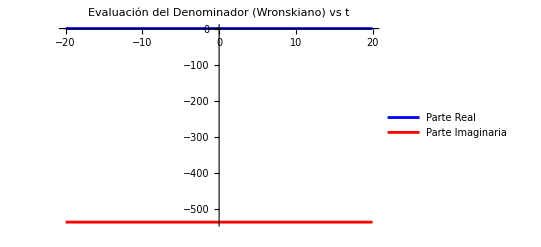

```mathematica
Plot[
{Re[denominador[t]],Im[denominador[t]]},
{t,-20,20},PlotStyle->{Blue,Red},
PlotLegends->{"Parte Real","Parte Imaginaria"},
PlotLabel->"Evaluación del Denominador (Wronskiano) vs t"]
```

```mathematica
denominador2[t_]:= ParabolicCylinderD[-(ⅈ δ)/2,ⅈ *z[t]] ParabolicCylinderD[(ⅈ δ)/2,z[t]]+ⅈ ParabolicCylinderD[-1-(ⅈ δ)/2,ⅈ *z[t]] (ParabolicCylinderD[1+(ⅈ δ)/2,z[t]]-z0 ParabolicCylinderD[(ⅈ δ)/2,z[t]])
```

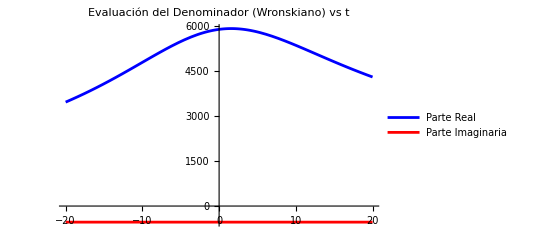

```mathematica
Plot[
{Re[denominador2[t]],Im[denominador[t]]},
{t,-20,20},PlotStyle->{Blue,Red},
PlotLegends->{"Parte Real","Parte Imaginaria"},
PlotLabel->"Evaluación del Denominador (Wronskiano) vs t"]
```

```mathematica
W=denominador[0];
```

### Comparison of solutions

```mathematica
β=0.25;
Ω=1.0;
δ = Ω^2/(2β^2);
t0=-10 Ω/β^2;
tf=10 Ω/β^2;

z[t_]:=β*Exp[-I*Pi/4]*t;
z0=z[t0];zf = z[tf];
```

```mathematica
numC1=Exp[-z0^2/4]*ParabolicCylinderD[-I*δ/2,I*z0];
numC2=Exp[-z0^2/4]*(ParabolicCylinderD[1+I*δ/2,z0]-z0*ParabolicCylinderD[I*δ/2,z0]);
```

```mathematica
C1=numC1/W;
C2=numC2/W;
```

```mathematica
vExact[t_]:=c1*ParabolicCylinderD[I*δ/2,z[t]]+c2*ParabolicCylinderD[-1-I*δ/2,I*z[t]];
```

```mathematica
condicionesVz={v[z0]==Exp[-z0^2/4],v'[z0]==-(z0/2)*Exp[-z0^2/4]};
solV=NDSolve[
{v''[t]+(β^4*t^2/4+Ω^2/4-I*β^2/2)*v[t]==0,v[t0]==Exp[I*β^2*t0^2/4],v'[t0]==I*(β^2*t0/2)*Exp[I*β^2*t0^2/4]},v,{t,t0,tf},MaxSteps->100000][[1]];

vNum[t_]:=v[t]/. solV;
```

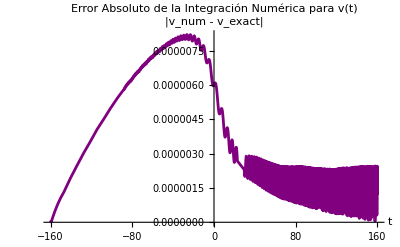

```mathematica
Plot[Abs[vNum[t]-vExact[t]],{t,t0,tf},PlotRange->All,PlotStyle->Purple,AxesLabel->{"t","|v_num - v_exact|"},PlotLabel->"Error Absoluto de la Integración Numérica para v(t)"]
```

```mathematica
condicionesU={u[t0]==1,u'[t0]==0};
condicionesVt={v[t0]==Exp[I*β^2*t0^2/4],v'[t0]==I*(β^2*t0/2)*Exp[I*β^2*t0^2/4]};
```

```mathematica
uExact[t_]:=vExact[t]*Exp[-I*β^2*t^2/4];
uExactDeriv[t_]=D[uExact[t],t];
alphaExact[t_]:=(2*I/Ω)*(uExactDeriv[t]/uExact[t]);
```

```mathematica
(*Ecuación:i α+'+(λ/2)(α+^2-1)-Δ(t)α+ =0*)solAlpha=NDSolve[{I*a'[t]+(Ω/2)*(a[t]^2-1)-(β^2*t)*a[t]==0,a[t0]==0},a,{t,t0,tf},MaxSteps->100000][[1]];
alphaNum[t_]:=a[t]/. solAlpha;
```

```mathematica
alphaErr[t_]:= Abs[alphaNum[t]-alphaExact[t]];
alphaRerr[t_]:= alphaErr[t]/Abs[alphaExact[t]];
```

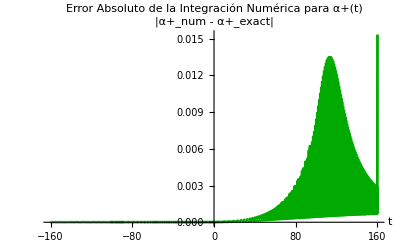

```mathematica
Plot[alphaErr[t],{t,t0,tf},PlotStyle->Darker[Green],AxesLabel->{"t","|α+_num - α+_exact|"},PlotLabel->"Error Absoluto de la Integración Numérica para α+(t)"]
```

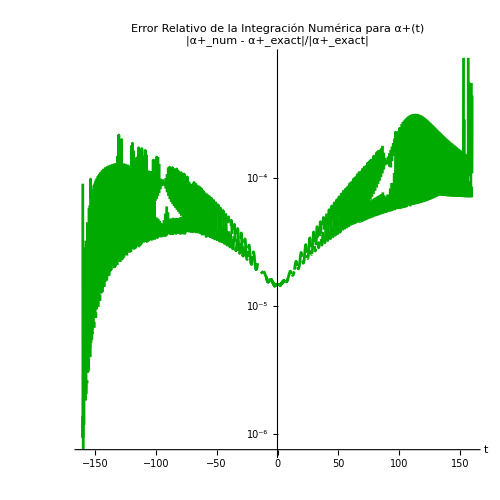

```mathematica
Plot[alphaRerr[t],{t,t0,tf},PlotStyle->Darker[Green],AxesLabel->{"t","|α+_num - α+_exact|/|α+_exact|"},PlotLabel->"Error Relativo de la Integración Numérica para α+(t)", ScalingFunctions->"Log", AspectRatio->1, ImageSize->500]
```

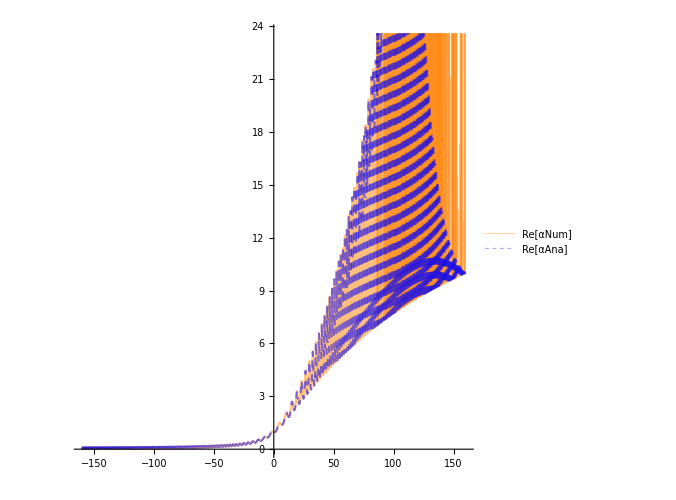

```mathematica
Plot[{Re[alphaNum[t]],Re[alphaExact[t]]},{t,t0,tf},
PlotStyle->{ Directive[Thickness[0.003], Orange, Opacity[0.5]], 
Directive[Dashed,Thickness[0.003],Blue, Opacity[0.5]]},
PlotLegends-> {"Re[αNum]", "Re[αAna]"},
AspectRatio->1, ImageSize->500]
```